## Appendix - Adaptive dynamics approximation

```mathematica
Quit[];
```

### Accessory functions

#### Two-patch model

```mathematica
(* Simulate the ecological dynamics of the resident *)
Simulate[x0_,n10_,n20_,a0_,b0_,h0_,s0_,d0_,m0_,α0_,T0_]:=Block[{t=0,n1=n10,n2=n20},
population=Reap[While[t≤T0,
Sow[{t,n1,n2}];
{n1,n2}=Λ.{n1,n2}/.Subscript[r, 1]->Subscript[r, 1][x0,x0]/.Subscript[r, 2]->Subscript[r, 2][x0,x0]/.a->a0/.b->b0/.h->h0/.s->s0/.d->d0/.m->m0/.α->α0/.Subscript[N, 1]->n1/.Subscript[N, 2]->n2;
t++;
]][[2]][[1]];
p1=ListLinePlot[{#[[1]],#[[2]]}&/@population,PlotRange->All,PlotStyle->RGBColor[0.5,0.5,0.5],PlotLegends->LineLegend[{"Patch 1"}]];
p2=ListLinePlot[{#[[1]],#[[3]]}&/@population,PlotRange->All,PlotStyle->RGBColor[0.7,0.7,0.7],PlotLegends->LineLegend[{"Patch 2"}]];
Show[p1,p2,AxesLabel->{"Generations","Population size"}]
]
```

```mathematica
(* Invasion analysis *)
PairwiseInvasibilityPlot[a0_,b0_,h0_,s0_,d0_,m0_,α0_,xmin_,xmax_,step_,nstart_,plotoptions_]:=Block[{pars={a->a0,b->b0,h->h0,s->s0,d->d0,m->m0,α->α0},fct,xvalues,combinations,eq,fitness,init,sols,N1,N2},
fct={Subscript[r, 1]->Subscript[r, 1][y,x],Subscript[r, 2]->Subscript[r, 2][y,x]};
xvalues=Range[xmin,xmax,step];
combinations=Tuples[xvalues,2];
eq={Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}/.fct/.pars;
fitness=λ/.fct/.pars;
init={{Subscript[N, 1],nstart},{Subscript[N, 2],nstart}};
sols=Map[FindRoot[eq/.y->x/.x->#,init]&,xvalues];
N1=Map[ConstantArray[#,Length[xvalues]]&,Subscript[N, 1]/.sols]//Flatten;
N2=Map[ConstantArray[#,Length[xvalues]]&,Subscript[N, 2]/.sols]//Flatten;
ListContourPlot[Reap[Map[Sow[{#[[1]],#[[2]],fitness/.x->#[[1]]/.y->#[[2]]/.Subscript[N, 1]->#[[3]]/.Subscript[N, 2]->#[[4]]}]&,MapThread[Flatten[{#1,#2,#3}]&,{combinations,N1,N2}]]][[2]][[1]],Contours->{1},FrameLabel->{"Resident trait value","Mutant trait value"},plotoptions]
]
PairwiseInvasibilityData[a0_,b0_,h0_,s0_,d0_,m0_,α0_,xmin_,xmax_,step_,nstart_,plotoptions_]:=Block[{pars={a->a0,b->b0,h->h0,s->s0,d->d0,m->m0,α->α0},fct,xvalues,combinations,eq,fitness,init,sols,N1,N2,header},
fct={Subscript[r, 1]->Subscript[r, 1][y,x],Subscript[r, 2]->Subscript[r, 2][y,x]};
xvalues=Range[xmin,xmax,step];
combinations=Tuples[xvalues,2];
eq={Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}/.fct/.pars;
fitness=λ/.fct/.pars;
init={{Subscript[N, 1],nstart},{Subscript[N, 2],nstart}};
sols=Map[FindRoot[eq/.y->x/.x->#,init]&,xvalues];
N1=Map[ConstantArray[#,Length[xvalues]]&,Subscript[N, 1]/.sols]//Flatten;
N2=Map[ConstantArray[#,Length[xvalues]]&,Subscript[N, 2]/.sols]//Flatten;
header={{"x","y","lambda"}};
Join[header,Reap[Map[Sow[{#[[1]],#[[2]],fitness/.x->#[[1]]/.y->#[[2]]/.Subscript[N, 1]->#[[3]]/.Subscript[N, 2]->#[[4]]}]&,MapThread[Flatten[{#1,#2,#3}]&,{combinations,N1,N2}]]][[2]][[1]]]
]
```

```mathematica
(* Stability analysis *)
FindSingularities[a0_,b0_,h0_,s0_,d0_,m0_,α0_,xmin_,xmax_,step_,nstart_,tol_]:=Block[{pars={a->a0,b->b0,h->h0,s->s0,d->d0,m->m0,α->α0},fct,eqs,gdt,xvalues=Range[xmin,xmax,step],gvalues, gratios,sng,dmg,bef,aft,isconv},
fct={Subscript[r, 1]->Subscript[r, 1][x,x],Subscript[r, 2]->Subscript[r, 2][x,x],Subscript[W, 1]->Subscript[W, 1][x,x],Subscript[W, 2]->Subscript[W, 2][x,x],Subscript[dW, 1]->Subscript[dW, 1][x],Subscript[dW, 2]->Subscript[dW, 2][x],Subscript[ddW, 1]->Subscript[ddW, 1][x],Subscript[ddW, 2]->Subscript[ddW, 2][x]};
eqs={Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}/.fct/.pars;
gdt=grad/.fct/.pars;
gvalues=Map[gdt/.x->#/.FindRoot[eqs/.x->#,{{Subscript[N, 1],nstart},{Subscript[N, 2],nstart}}]&,xvalues];
gratios={1,Ratios[gvalues]}//Flatten;
sng=Select[MapThread[If[#1<0,#2,{}]&,{gratios,xvalues}],UnsameQ[#,{}]&];
dmg=Map[FindRoot[eqs/.x->#,{{Subscript[N, 1],nstart},{Subscript[N, 2],nstart}}]&,sng];
bef=Map[gdt/.x->#-step/.FindRoot[eqs/.x->#-step,{{Subscript[N, 1],nstart},{Subscript[N, 2],nstart}}]&,sng];
aft=Map[gdt/.x->#+step/.FindRoot[eqs/.x->#+step,{{Subscript[N, 1],nstart},{Subscript[N, 2],nstart}}]&,sng];
isconv=MapThread[#1-#2>0&&Sign[#1]≠Sign[#2]&,{bef,aft}];
MapThread[{#1,Subscript[N, 1]/.#2,Subscript[N, 2]/.#2,#3,curv/.fct/.pars/.x->#1/.#2}&,{sng,dmg,isconv}]
]
```

```mathematica
(* Visualize the selection gradient *)
PlotSelectionGradient[a0_,b0_,h0_,s0_,d0_, m0_,α0_,xmin_,xmax_,step_,nstart_,plotoptions_]:=Block[{pars={a->a0,b->b0,h->h0,s->s0,d->d0,m->m0,α->α0},gdt,eqs,fct},
fct={Subscript[r, 1]->Subscript[r, 1][x,x],Subscript[r, 2]->Subscript[r, 2][x,x],Subscript[W, 1]->Subscript[W, 1][x,x],Subscript[W, 1]->Subscript[W, 2][x,x],Subscript[dW, 1]->Subscript[dW, 1][x],Subscript[dW, 2]->Subscript[dW, 2][x],Subscript[ddW, 1]->Subscript[ddW, 1][x],Subscript[ddW, 2]->Subscript[ddW, 2][x]};
eqs={{Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}}/.fct/.pars;
gdt=grad/.fct/.pars;
ListLinePlot[Reap[Map[Sow[{#,gdt/.x->#}/.FindRoot[eqs/.x->#,{{Subscript[N, 1],nstart},{Subscript[N, 2],nstart}}]]&,Range[xmin,xmax,step]]][[2]][[1]],AxesLabel->{"Resident trait value","Selection gradient"},plotoptions]
]
```

```mathematica
(* Singularity search and stability analysis across parameter space *)
ExploreParameterSpace[a0_,b0_,h0_,s0_,d0_,m0_,α0_,xmin_,xmax_,step_,nstart_,tol_]:=Block[{cbn,sng,header},
cbn=Tuples[{a0,b0,h0,s0,d0,m0,α0}];
sng=Map[FindSingularities[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],xmin,xmax,step,nstart,tol]&,cbn];
header={{"a","b","h","s","d","m","alpha","x","N1","N2","isconv","curv"}};
Join[header,MapThread[ArrayFlatten[{{#1,#2}}]&,{MapThread[ConstantArray[#1,Length[#2]]&,{cbn,sng}],sng}]//Catenate]
]
```

#### One-patch model

```mathematica
(* One-patch invasion analysis *)
PairwiseInvasibilityPlotLocal[a1_,a2_, b0_,s0_,d0_,α0_,xmin_,xmax_,step_,nstart_,plotoptions_]:=Block[{pars={Subscript[a, 1]->a1,Subscript[a, 2]->a2,b->b0,s->s0,d->d0,α->α0},xvalues,combinations,eq,fitness,init,sols,Neq},
xvalues=Range[xmin,xmax,step];
combinations=Tuples[xvalues,2];
eq=r[y,x]==1/.pars;
fitness=r[y,x]/.pars;
init={N,nstart};
sols=Map[FindRoot[eq/.y->x/.x->#,init]&,xvalues];
Neq=Map[ConstantArray[#,Length[xvalues]]&,N/.sols]//Flatten;
ListContourPlot[Reap[Map[Sow[{#[[1]],#[[2]],fitness/.x->#[[1]]/.y->#[[2]]/.N->#[[3]]}]&,MapThread[Flatten[{#1,#2}]&,{combinations,Neq}]]][[2]][[1]],Contours->{1},FrameLabel->{"Resident trait value","Mutant trait value"},plotoptions]
]
```

```mathematica
(* Plot the selection gradient within one patch *)
PlotSelectionGradientLocal[a1_,a2_,b0_,s0_,d0_,α0_,xmin_,xmax_,step_,nstart_,plotoptions_]:=Block[{pars={Subscript[a, 1]->a1, Subscript[a, 2]->a2,b->b0,s->s0,d->d0,α->α0},gdt,eqs,fct},
eq=r[x,x]==1/.pars;
gdt=D[W[y,x],y]/.y->x/.pars;
ListLinePlot[Reap[Map[Sow[{#,gdt/.x->#}/.FindRoot[eq/.x->#,{N,nstart}]]&,Range[xmin,xmax,step]]][[2]][[1]],AxesLabel->{"Resident trait value","Selection gradient"},plotoptions]
]
```

```mathematica
(* One-patch singularity search *)
FindSingularitiesLocal[a1_,a2_,b0_,s0_,d0_,α0_,xmin_,xmax_,step_,nstart_,tol_]:=Block[{pars={Subscript[a, 1]->a1,Subscript[a, 2]->a2,b->b0,s->s0,d->d0,α->α0},eq,gdt,xvalues=Range[xmin,xmax,step],gvalues, gratios,sng,dmg,bef,aft,isconv},
eq=r[x,x]==1/.pars;
gdt=D[W[y,x],y]/.y->x/.pars;
gvalues=Map[gdt/.x->#/.FindRoot[eq/.x->#,{N,nstart}]&,xvalues];
gratios={1,Ratios[gvalues]}//Flatten;
sng=Select[MapThread[If[#1<0,#2,{}]&,{gratios,xvalues}],UnsameQ[#,{}]&];
dmg=Map[FindRoot[eq/.x->#,{N,nstart}]&,sng];
bef=Map[gdt/.x->#-step/.FindRoot[eq/.x->#-step,{N,nstart}]&,sng];
aft=Map[gdt/.x->#+step/.FindRoot[eq/.x->#+step,{N,nstart}]&,sng];
isconv=MapThread[#1-#2>0&&Sign[#1]≠Sign[#2]&,{bef,aft}];
MapThread[{#1,N/.#2,#3,D[D[W[y,x],y],y]/.y->x/.pars/.x->#1/.#2}&,{sng,dmg,isconv}]
]
```

```mathematica
(* Explore parameter space in the one-patch model *)
ExploreParameterSpaceLocal[a1_,a2_,b0_,s0_,d0_,α0_,xmin_,xmax_,step_,nstart_,tol_]:=Block[{cbn,sng,header},
cbn=Tuples[{a1,a2,b0,s0,d0,α0}];
sng=Map[FindSingularitiesLocal[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],xmin,xmax,step,nstart,tol]&,cbn];
header={{"a1","a2","b","s","d","alpha","x","N","isconv","curv"}};
Join[header,MapThread[ArrayFlatten[{{#1,#2}}]&,{MapThread[ConstantArray[#1,Length[#2]]&,{cbn,sng}],sng}]//Catenate]
]
```

### Parametrization

Here we introduce a set of default parameters that we will use throughout this script to check assumptions and the validity of our derivations. You can change those values. We also introduce a list of 
rules to replace functions by their definitions in during expression evaluation.

```mathematica
default={a->400,b->100,h->0.5,s->1,d->0.2,m->0.01,α->1};
functions={Subscript[r, 1]->Subscript[r, 1][y,x],Subscript[r, 2]->Subscript[r, 2][y,x],Subscript[W, 1]->Subscript[W, 1][y,x],Subscript[W, 2]->Subscript[W, 2][y,x],Subscript[dW, 1]->Subscript[dW, 1][x],Subscript[dW, 2]->Subscript[dW, 2][x],Subscript[ddW, 1]->Subscript[ddW, 1][x],Subscript[ddW, 2]->Subscript[ddW, 2][x]};
```

### Resident population dynamics

This script accompanies the appendix of the article. Consider a population that is monomorphic with respect to the ecological trait x. The transition matrix of the population dynamics is given by

```mathematica
Λ ={{1-m,m},{m,1-m}}.{{Subscript[r, 1],0},{0,Subscript[r, 2]}};
%//MatrixForm
```

((1-m) r_1 | m r_2
m r_1 | (1-m) r_2)

where r_j=r_j(y,x) is the within-patch geometric growth rate of the mutant.

```mathematica
Subscript[r, 1][y_,x_]:=1-d+1/2 Subscript[W, 1][y,x](1+A[y,x])
Subscript[r, 2][y_,x_]:=1-d+1/2 Subscript[W, 2][y,x](1+A[y,x])
```

where the attractiveness is given by

```mathematica
A[y_,x_]:=Exp[-α(y-x)^2]
```

and the reproductive success W_j in patch j is given by

```mathematica
Subscript[W, 1][y_,x_]:=Subscript[e, 1][y]Subscript[R, 11][x]+Subscript[e, 2][y]Subscript[R, 21][x]
Subscript[W, 2][y_,x_]:=Subscript[e, 1][y]Subscript[R, 12][x]+Subscript[e, 2][y]Subscript[R, 22][x]
```

where e_i is the attack rate of the organisms on resource i. The resources follow dynamics of the following form:

```mathematica
R'[t]==a-(b+N e) R[t];
```

Where a is the resource inflow rate, b is the resource outflow rate, N is the consumer population size and e is the attack rate of the consumer. Assuming that the dynamics of the resources are fast relative to the consumer population dynamics, the equilibrium resource concentrations have the form

```mathematica
resources=Solve[a-(b + N e) R == 0,R]
```

{{R→a/(b+e N)}}

The equilibrium resource concentration R_ij of resource i in patch j are therefore given by

```mathematica
Subscript[R, 11][x_]:=R/.resources/.e->Subscript[e, 1][x]/.N->Subscript[N, 1]//First
Subscript[R, 12][x_]:=h R/.resources/.e->Subscript[e, 1][x]/.N->Subscript[N, 2]//First
Subscript[R, 21][x_]:=h R/.resources/.e->Subscript[e, 2][x]/.N->Subscript[N, 1]//First
Subscript[R, 22][x_]:=R/.resources/.e->Subscript[e, 2][x]/.N->Subscript[N, 2]//First
```

where the attack rates are given by

```mathematica
Subscript[e, 1][x_]:=Exp[-s(x+1)^2]
Subscript[e, 2][x_]:=Exp[-s(x-1)^2]
```

where s is the ecological selection coefficient. We can simulate the ecological dynamics in the two patches for a population with given parameter, trait values, and starting densities,

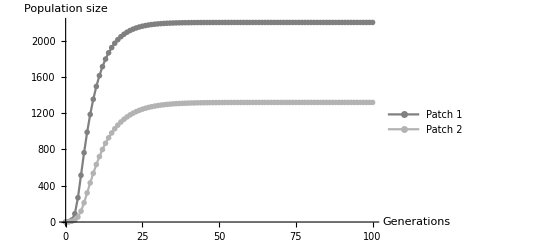

```mathematica
Simulate[-1,1,1,400,100,0.5,1,0.2,0,0,100]
```

### Invasion analysis of a mutant

The invasion fitness of a mutant is the leading eigenvalue of the transition matrix. Here we assume that the mutant is initially at low density, sufficiently so that it does not affect the resource dynamics and therefore the density-dependence component of the population dynamics. The invasion fitness is

```mathematica
λ=Λ//Eigenvalues//Last
```

1/2 (r_1-m r_1+r_2-m r_2+√((-r_1+m r_1-r_2+m r_2)^2-4 (r_1 r_2-2 m r_1 r_2)))

And we can visualize the pairwise invasibility of various mutants for various residents given parameter values.

```mathematica
PairwiseInvasibilityPlot[400,100,1,0.01,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet
```

-Graphics-

We check that at the equilibrium of the population dynamics the mutant is extinct, i.e. we are interested in the stability of this equilibrium to know if the mutant can invade. Let M_j be the density of the mutant in patch j.

```mathematica
Solve[{Subscript[M, 1],Subscript[M, 2]}==Λ.{Subscript[M, 1],Subscript[M, 2]}/.functions/.default/.x->0,{Subscript[M, 1],Subscript[M, 2]}]
```

{{M_1→0.,M_2→0.}}

We also check that the invasion fitness of the resident is one.

```mathematica
λ/.functions/.y->x/.default/.x->0/.Solve[{{Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}/.functions/.y->x/.default/.x->0,Subscript[N, 1]>0,Subscript[N, 2]>0},{Subscript[N, 1],Subscript[N, 2]}]//Quiet
```

{1.}

### Selection gradient

The selection gradient is the derivative of the invasion fitness with respect to the mutant phenotype, evaluated at the resident phenotype. It indicates the strength and direction of selection. In the appendix we derived the following formula for the selection gradient:

```mathematica
grad=v.{{1-m,m}, {m,1-m}}.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.u/(v.u);
```

where u and v are the right and left dominant eigenvectors of the transition matrix, respectively. They are given by

```mathematica
u=(Λ//Eigenvectors//Last) m Subscript[r, 1];
v=(Λ//Transpose//Eigenvectors//Last) m Subscript[r, 2];
```

which can be re-written in terms of λ:

```mathematica
λ-(1-m)Subscript[r, 2]==v[[1]]==u[[1]] //Simplify
v[[1]]=λ-(1-m)Subscript[r, 2];
u[[1]]=λ-(1-m)Subscript[r, 2];
```

True

And the selection gradient simplifies to

```mathematica
grad=grad/.λ->1//Simplify
```

(m^2 dW_2 r_1+dW_1 (1-m-(2-4 m+m^2) r_2+(1-3 m+2 m^2) r_2^2))/(1+(-2+2 m+m^2 r_1) r_2+(-1+m)^2 r_2^2)

where

```mathematica
Subscript[dW, 1][x_]:=D[Subscript[W, 1][y,x],y]/.y->x;
Subscript[dW, 2][x_]:=D[Subscript[W, 2][y,x],y]/.y->x;
```

We check that this expression is equivalent to differentiating the invasion fitness function:

```mathematica
grad/.functions/.y->x/.default/.x->0/.Solve[{{Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}/.functions/.y->x/.default/.x->0,Subscript[N, 1]>0,Subscript[N, 2]>0},{Subscript[N, 1],Subscript[N, 2]}]//Quiet
D[λ/.functions,y]/.y->x/.default/.x->0/.Solve[{{Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}/.functions/.y->x/.default/.x->0,Subscript[N, 1]>0,Subscript[N, 2]>0},{Subscript[N, 1],Subscript[N, 2]}]//Quiet
```

{7.30142×10^-15}

{-2.77556×10^-17}

### Fitness curvature at the singularity

We also derived an expression for the fitness curvature an an evolutionarily singular point, i.e. a trait value for which the selection gradient is zero,

```mathematica
curv=(dv.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.u + v.M.{{Subscript[ddW, 1]-α Subscript[W, 1],0},{0,Subscript[ddW, 2]-α Subscript[W, 2]}}.u + v.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.du)/(v.u);
```

where

```mathematica
dv={(m-1)Subscript[dW, 2],m Subscript[dW, 2]};
du={(m-1)Subscript[dW, 2],m Subscript[dW, 1]};
M={{1-m,m},{m,1-m}};
```

The fitness curvature therefore simplifies to

```mathematica
curv/.λ->1//Simplify
```

1/(1+(-2+2 m+m^2 r_1) r_2+(-1+m)^2 r_2^2)(m^2 ddW_2 r_1+2 (-1+2 m) dW_1 dW_2 (1+(-1+m) r_2)+ddW_1 (1-m-(2-4 m+m^2) r_2+(1-3 m+2 m^2) r_2^2)-α W_1+m α W_1+2 α r_2 W_1-4 m α r_2 W_1+m^2 α r_2 W_1-α r_2^2 W_1+3 m α r_2^2 W_1-2 m^2 α r_2^2 W_1-m^2 α r_1 W_2)

where

```mathematica
Subscript[ddW, 1][x_]:=D[D[Subscript[W, 1][y,x],y],y]/.y->x;
Subscript[ddW, 2][x_]:=D[D[Subscript[W, 2][y,x],y],y]/.y->x;
```

We check that this is indeed the curvature of the invasion fitness function at the evolutionary singular point given some parameter values,

```mathematica
curv/.functions/.y->x/.default/.FindRoot[{{Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]},grad==0}/.functions/.y->x/.default,{{Subscript[N, 1],1000},{Subscript[N, 2],1000},{x,-1}}]//Quiet
D[D[λ/.functions,y],y]/.y->x/.default/.FindRoot[{{Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]},grad==0}/.functions/.y->x/.default,{{Subscript[N, 1],1000},{Subscript[N, 2],1000},{x,-1}}]//Quiet
```

1.94222

1.94222

### Evolutionary stability analysis

Given a set of parameters, we can summarize the pairwise invasibility plot by its singular points, i.e. where the selection gradient cancels out. We use functions to numerically explore the selection gradient across resident trait values and find the singular trait values. We then analyze the stability of each singular point, or equilibrium, in two ways. The singular point is convergence stable, i.e. attainable, if the selection gradient goes from positive to negative at the singular point. That is, if selection favors higher trait values when below the singular point, but lower trait values when above the singular point. We approximate the derivative of the selection gradient at the singular point by the difference in selection gradient close to the singularity. (The exact derivative is difficult to derive because it depends on how a change in trait value affects the equilibrium population densities, because of density-dependence in the model, and we could not find an explicit expression for those.) The singular point is evolutionarily stable, i.e. invasion-proof, if the curvature of the fitness function is negative at the singular point, that is, the singular point is a local fitness maximum.

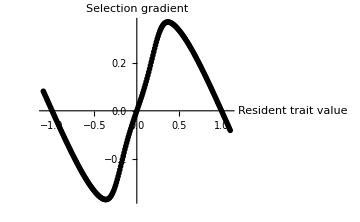
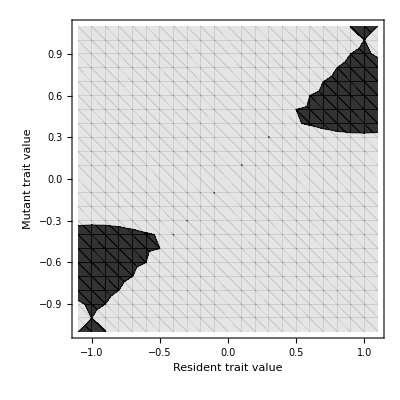

{{-0.99,1902.86,302.915,True,5.60637},{0.,1661.09,1661.09,False,284446.},{1.,302.71,1902.66,True,-7.88127}}

```mathematica
p1=PlotSelectionGradient[400,100,0.2,2.0,0.2,0.000001,0,-1.1,1.1,0.01,1000,ImageSize->Medium]//Quiet;
p2=PairwiseInvasibilityPlot[400,100,0.2,2.0,0.2,0.000001,0,-1.1,1.1,0.1,1000,{}] //Quiet;
{p1,p2}
FindSingularities[400,100,0.2,2.0,0.2,0.000001,0,-1.1,1.1,0.01,1000,0.03]//Quiet
```

### Extensive exploration of parameter space

We now apply the singularity search procedure and the stability analysis across various values of the parameters of interest.

```mathematica
results=ExploreParameterSpace[{400},{100},Range[0,1,0.1],Range[0.01,2.5,0.1],{0.2},{0.000001},{1},-1.1,1.1,0.01,1000,0.001]//Quiet;
(* Note: This algorithm cannot calculate the sequential ratio it needs to tell whether the selection gradient changes sign, whenever it encounters a selection gradient of exactly zero. But this did not influence the results because the ratio calculation that comes right before the problematic one has zero at the numerator, and can catch the singularity. *)
(* Data were generated one block at a time for different parameter values *)
```

$Aborted

```mathematica
Export["adaptive_dynamics.csv",results,"CSV"];
```

### Generating a few pairwise invasibility plots

```mathematica
Export["pip1.csv",PairwiseInvasibilityData[400,100,1,0.01,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet,"CSV"];
Export["pip2.csv",PairwiseInvasibilityData[400,100,1,0.5,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet,"CSV"];
Export["pip3.csv",PairwiseInvasibilityData[400,100,1,1,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet,"CSV"];
Export["pip4.csv",PairwiseInvasibilityData[400,100,1,1.5,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet,"CSV"];
Export["pip5.csv",PairwiseInvasibilityData[400,100,1,2,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet,"CSV"];
Export["pip6.csv",PairwiseInvasibilityData[400,100,1,2.5,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet,"CSV"];
Export["pip7.csv",PairwiseInvasibilityData[400,100,1,3,0.2,0.01,0,-1,1,0.01,1000,{}]//Quiet,"CSV"];
```

### Special case without gene flow

Assume that there is now no dispersal at all between the two patches, which are effectively evolving independently from each other. The dispersal rate and the habitat symmetry parameter are now irrelevant. The invasion fitness of the mutant is now its local growth rate:

```mathematica
r[y_,x_]:=1-d+W[y,x](1+A[y,x]);
```

where

```mathematica
W[y_,x_]:=Subscript[e, 1][y]Subscript[R, 1][x]+Subscript[e, 2][y]Subscript[R, 2][x];
```

where the equilibrium resource concentrations are

```mathematica
Subscript[R, 1][x_]:=R/.resources/.e->Subscript[e, 1][x]/.a->Subscript[a, 1]//First
Subscript[R, 2][x_]:=R/.resources/.e->Subscript[e, 2][x]/.a->Subscript[a, 2]//First
```

We can conduct a pairwise invasion analysis within this patch,

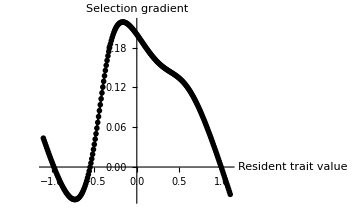
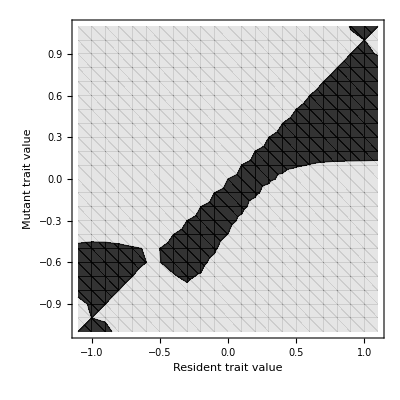

{{-0.97,912.705,True,-0.319586},{-0.54,1158.56,False,0.7589},{1.,2910.,True,-0.378738}}

```mathematica
p1=PlotSelectionGradientLocal[100,300,100,2.0,0.2,0,-1.1,1.1,0.01,1000,ImageSize->Medium]//Quiet;
p2=PairwiseInvasibilityPlotLocal[100,300,100,2.0,0.2,0,-1.1,1.1,0.1,1000,{}] //Quiet;
{p1,p2}
FindSingularitiesLocal[100,300,100,2.0,0.2,0,-1.1,1.1,0.01,1000,0.03]//Quiet
```

And we can explore parameter space

```mathematica
(*Launch before going to bed*)
```

```mathematica
results=ExploreParameterSpaceLocal[{400},Range[0,1,0.01]*400,{100},Range[0.01,2.5,0.01],{0.2},{0,1,10},-1.1,1.1,0.01,1000,0.001]//Quiet;
```

```mathematica
Export["adaptive_dynamics_patch1.csv",results, "CSV"];
```

```mathematica
results=ExploreParameterSpaceLocal[Range[0,1,0.01]*400,{400},{100},Range[0.01,2.5,0.01],{0.2},{0,1,10},-1.1,1.1,0.01,1000,0.001]//Quiet;
```

```mathematica
Export["adaptive_dynamics_patch2.csv",results, "CSV"];
```